```mathematica
(* Get["/Users/robert/Documents/MyMathematicaPrograms/DimIrrepsProj/DimIrrepsLie.wl"]; *)
```

```mathematica
Get["…/src/DimIrrepsLie.wl"](* On GitHub *)
```

### Details

The dimension of an irreducible representation of the Lie algebra G, characterized by its highest weight, is obtained from the Weyl dimension formula. 
This formula involves the product over all the positive roots of the inner products between them and the chosen weight, shifted by the Weyl vector.
The collection of inner products is encoded by labels attached to the vertices of the the periodic quiver of roots.
For simply - laced Lie algebras (ADE cases) this quiver is obtained from the adjacency matrix of the Dynkin diagram and from the matrices that describe the fusion algebra of SU (2) at an appropriate level. For non simply - laced cases the calculation is similar but it involves specific scaling factors for the Coxeter orbits of short and long roots.

The syntax DimensionIrrepLie["G", list] uses the above algorithm, for all choices of the Lie algebra G. 
The second argument, list, is the list of components of the highest weight of the chosen irreducible representation in the basis of fundamental weights.
If the first argument is dropped, G=Ar is assumed. However, if the first argument is absent (so G is assumed to be Ar=su(r+1)) the program does not use the general algorithm described before to determine the dimension; rather it uses the following explicit expression (which actually comes from using the previous algorithm), where r denotes the rank and where the list of components is denoted (x_j):

```mathematica
(∏_(p=1)^r (∏_(s=1)^(1-p+r) (p+∑_(j=s)^(-1+p+s) Subscript[x, j])))/BarnesG[2+r]
```

Standard notations for classical groups and their Lie algebras: 
Ar = su(r+1), the Lie algebras of the special unitary groups.
Dr = so(2r), the Lie algebras of the special orthogonal groups (even case).
Br = so(2r+1), the Lie algebras of the special orthogonal groups (odd case).
Cr = sp(r)=usp(2r), the Lie algebras of the (compact) symplectic groups.
Exceptional simple Lie groups: E6, E7, E8, G2, F4.

Ordering of fundamental weights, in the list of components, is determined by the ordering of vertices of the associated Dynkin diagram, or by the list of simple roots.
This order is standard (from left to right) for Ar. The two special simple roots of Dr are the last two. The special simple root in E6, E7, or E8, is the last one. 
Non simply-laced cases: For Br, the last root to the right is the unique short simple root. For G2, the short simple root is also to the right. For Cr, the short roots (all simple roots but one) are to the left. For F4 there should be no ambiguity. The ordering can also be inferred from the dimensions of fundamental representations (see the Examples section).

The syntax DimensionIrrepLie["G", list, q] calculating the q-dimension uses the same algorithm as in the classical case, but the inner products associated with the vertices of the periodic quiver of roots are calculated in terms of q-numbers. The result is expressed in terms of variables qnum[n,q] which have no value but represent the q-numbers n, defined as (q^n - q^(-n))/(q-q^(-1)). 
The q-dimension can be obtained in terms of q by substituting (using Rule) qnum[n,q] to the previous expression. See Examples. 
The formal variable q can be taken real, or specialised to a complex root of unity Exp[(ⅈ π)/κ], but in the latter case the variable κ should be large enough for the chosen irrep to exist.
The classical situation (usual dimensions) is recovered when q goes to 1.

### Basic Examples

The Lie algebra Ar is the default:

```mathematica
DimensionIrrepLie[{a,b}](* A2 = su(3) *)
```

1/2 (1+a) (1+b) (2+a+b)

Various types of Lie algebras:

```mathematica
DimensionIrrepLie ["D5",{1,0,0,0,0}] (* Vectorial representation of so(10) *)
```

10

```mathematica
DimensionIrrepLie ["D5",{0,0,0,0,1}] (* Half-spinor representation of so(10) *)
```

16

```mathematica
DimensionIrrepLie ["D5",{0,0,0,1,0}] (* Half-spinor representation of so(10) *)
```

16

```mathematica
DimensionIrrepLie ["E6",{2,5,13,4,11,18}]
```

199815954869278740594812606136365625

```mathematica
DimensionIrrepLie ["G2",{a,b}]
```

9/40 (1+a) (1/3+b/3) (4/3+a+b/3) (5/3+a+(2 b)/3) (2+a+b) (3+2 a+b)

Quantum dimension (numeric):

```mathematica
DimensionIrrepLie["A3",{2,5,3},q]
```

(qnum[4,q] qnum[6,q] qnum[9,q] qnum[10,q] qnum[13,q])/(qnum[1,q]^3 qnum[2,q]^2)

```mathematica
%/. {qnum[n_,q] :> Subscript[Row[{"(",n,")"}],q]}
```

((4)_q (6)_q (9)_q (10)_q (13)_q)/((1)_q^3 (2)_q^2)

Quantum dimension (symbolic):

```mathematica
DimensionIrrepLie["A3",{a,b,c},q]
```

(qnum[1+a,q] qnum[1+b,q] qnum[2+a+b,q] qnum[1+c,q] qnum[2+b+c,q] qnum[3+a+b+c,q])/(qnum[1,q]^3 qnum[2,q]^2 qnum[3,q])

```mathematica
%/. {qnum[n_,q] :> Subscript[Row[{"(",n,")"}],q]}
```

((1+a)_q (1+b)_q (2+a+b)_q (1+c)_q (2+b+c)_q (3+a+b+c)_q)/((1)_q^3 (2)_q^2 (3)_q)

```mathematica
%%/. {qnum[n_, q] :> (q^n - q^(-n)) / (q - q^(-1))}//Simplify
```

(q^(-3 a-4 b-3 c) (-1+q^(2+2 a)) (-1+q^(2 (2+a+b))) (-1+q^(2+2 b)) (-1+q^(2 (2+b+c))) (-1+q^(2 (3+a+b+c))) (-1+q^(2+2 c)))/((-1+q^2)^6 (1+q^2)^2 (1+q^2+q^4))

Recovering the classical limit q -> 1:

```mathematica
DimensionIrrepLie["A3",{2,5,3},q];
```

```mathematica
%/. { qnum[n_, q] :> (q^n - q^(-n))/(q - q^(-1)) } //Simplify
```

((-1/q^6+q^6) (-1+q^8) (-1/q^9+q^9) (-1+q^20) (-1+q^26))/(q^23 (-1/q+q)^3 (-1+q^4)^2)

```mathematica
Limit[%, q->1]
```

7020

```mathematica
DimensionIrrepLie["A3",{2,5,3}]
```

7020

Same Lie algebra case as before, but symbolic:

```mathematica
DimensionIrrepLie["A3",{a,b,c},q];
```

```mathematica
%/.{ qnum[n_, q] :> (q^n - q^(-n))/(q - q^(-1)) } //Simplify
```

(q^(-3 a-4 b-3 c) (-1+q^(2+2 a)) (-1+q^(2 (2+a+b))) (-1+q^(2+2 b)) (-1+q^(2 (2+b+c))) (-1+q^(2 (3+a+b+c))) (-1+q^(2+2 c)))/((-1+q^2)^6 (1+q^2)^2 (1+q^2+q^4))

```mathematica
Limit[%, q->1]
```

1/12 (1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c)

```mathematica
DimensionIrrepLie["A3",{a,b,c}]
```

1/12 (1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c)

### Applications

#### Classical dimensions (symbolic)

The Lie algebra is Ar, r = 2, 3, 4, …:

```mathematica
DimensionIrrepLie[Table[Subscript[x,j],{j,1,2} ]]
```

1/2 (1+x_1) (1+x_2) (2+x_1+x_2)

```mathematica
DimensionIrrepLie[Table[Subscript[x,j],{j,1,3} ]]
```

1/12 (1+x_1) (1+x_2) (2+x_1+x_2) (1+x_3) (2+x_2+x_3) (3+x_1+x_2+x_3)

```mathematica
DimensionIrrepLie[Table[Subscript[x,j],{j,1,4} ]]
```

1/288 (1+x_1) (1+x_2) (2+x_1+x_2) (1+x_3) (2+x_2+x_3) (3+x_1+x_2+x_3) (1+x_4) (2+x_3+x_4) (3+x_2+x_3+x_4) (4+x_1+x_2+x_3+x_4)

With the above syntax the following equality is used:

```mathematica
Table[With[{r=rval},DimensionIrrepLie[Table[Subscript[x,j],{j,1,r} ]]==(∏_(p=1)^r (∏_(s=1)^(1-p+r) (p+∑_(j=s)^(-1+p+s) Subscript[x, j])))/BarnesG[2+r]],{rval,1,7}]
```

{True,True,True,True,True,True,True}

```mathematica
DimensionIrrepLie[{a,b,c}]//Timing
```

{0.000153,1/12 (1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c)}

```mathematica
DimensionIrrepLie["A3", {a,b,c}]//Timing  (* first call *)
```

{0.000129,1/12 (1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c)}

```mathematica
DimensionIrrepLie["A3", {a,b,c}]//Timing (* second call *)
```

{0.000116,1/12 (1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c)}

Other examples of Lie algebras:

```mathematica
DimensionIrrepLie["G2", {a,b}]
```

9/40 (1+a) (1/3+b/3) (4/3+a+b/3) (5/3+a+(2 b)/3) (2+a+b) (3+2 a+b)

```mathematica
DimensionIrrepLie["B3", {a,b,c}]
```

1/90 (1+a) (1+b) (2+a+b) (1/2+c/2) (3/2+b+c/2) (5/2+a+b+c/2) (2+b+c) (3+a+b+c) (4+a+2 b+c)

```mathematica
DimensionIrrepLie["C3", {a,b,c}]
```

1/90 (1/2+a/2) (1+a/2+b/2) (1+b) (1+c) (3/2+b/2+c) (2+b+c) (3+a+b+c) (4+a+b+2 c) (5+a+2 b+2 c)

```mathematica
DimensionIrrepLie["D4", {a,b,c,d}]
```

1/4320(1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c) (1+d) (2+b+d) (3+a+b+d) (3+b+c+d) (4+a+b+c+d) (5+a+2 b+c+d)

```mathematica
DimensionIrrepLie["A6", Table[Subscript[x,j],{j,1,6} ]]
```

1/24883200(1+x_1) (1+x_2) (2+x_1+x_2) (1+x_3) (2+x_2+x_3) (3+x_1+x_2+x_3) (1+x_4) (2+x_3+x_4) (3+x_2+x_3+x_4) (4+x_1+x_2+x_3+x_4) (1+x_5) (2+x_4+x_5) (3+x_3+x_4+x_5) (4+x_2+x_3+x_4+x_5) (5+x_1+x_2+x_3+x_4+x_5) (1+x_6) (2+x_5+x_6) (3+x_4+x_5+x_6) (4+x_3+x_4+x_5+x_6) (5+x_2+x_3+x_4+x_5+x_6) (6+x_1+x_2+x_3+x_4+x_5+x_6)

```mathematica
DimensionIrrepLie["E6", Table[Subscript[x,j],{j,1,6} ]]
```

1/23361421521715200000(1+x_1) (1+x_2) (2+x_1+x_2) (1+x_3) (2+x_2+x_3) (3+x_1+x_2+x_3) (1+x_4) (2+x_3+x_4) (3+x_2+x_3+x_4) (4+x_1+x_2+x_3+x_4) (1+x_5) (2+x_4+x_5) (3+x_3+x_4+x_5) (4+x_2+x_3+x_4+x_5) (5+x_1+x_2+x_3+x_4+x_5) (1+x_6) (2+x_3+x_6) (3+x_2+x_3+x_6) (4+x_1+x_2+x_3+x_6) (3+x_3+x_4+x_6) (4+x_2+x_3+x_4+x_6) (5+x_1+x_2+x_3+x_4+x_6) (5+x_2+2 x_3+x_4+x_6) (6+x_1+x_2+2 x_3+x_4+x_6) (7+x_1+2 x_2+2 x_3+x_4+x_6) (4+x_3+x_4+x_5+x_6) (5+x_2+x_3+x_4+x_5+x_6) (6+x_1+x_2+x_3+x_4+x_5+x_6) (6+x_2+2 x_3+x_4+x_5+x_6) (7+x_1+x_2+2 x_3+x_4+x_5+x_6) (8+x_1+2 x_2+2 x_3+x_4+x_5+x_6) (7+x_2+2 x_3+2 x_4+x_5+x_6) (8+x_1+x_2+2 x_3+2 x_4+x_5+x_6) (9+x_1+2 x_2+2 x_3+2 x_4+x_5+x_6) (10+x_1+2 x_2+3 x_3+2 x_4+x_5+x_6) (11+x_1+2 x_2+3 x_3+2 x_4+x_5+2 x_6)

```mathematica
DimensionIrrepLie["F4", Table[Subscript[x,j],{j,1,4} ]]
```

1/5893965000(1+x_1) (1+x_2) (2+x_1+x_2) (1/2+x_3/2) (3/2+x_2+x_3/2) (5/2+x_1+x_2+x_3/2) (2+x_2+x_3) (3+x_1+x_2+x_3) (4+x_1+2 x_2+x_3) (1/2+x_4/2) (1+x_3/2+x_4/2) (2+x_2+x_3/2+x_4/2) (3+x_1+x_2+x_3/2+x_4/2) (5/2+x_2+x_3+x_4/2) (7/2+x_1+x_2+x_3+x_4/2) (9/2+x_1+2 x_2+x_3+x_4/2) (5+x_1+2 x_2+(3 x_3)/2+x_4/2) (3+x_2+x_3+x_4) (4+x_1+x_2+x_3+x_4) (5+x_1+2 x_2+x_3+x_4) (11/2+x_1+2 x_2+(3 x_3)/2+x_4) (6+x_1+2 x_2+2 x_3+x_4) (7+x_1+3 x_2+2 x_3+x_4) (8+2 x_1+3 x_2+2 x_3+x_4)

#### Fundamental representations of exceptional simple Lie algebras

```mathematica
Table[DimensionIrrepLie ["E6",UnitVector[6,p]], {p, 1,6}]
```

{27,351,2925,351,27,78}

```mathematica
Table[DimensionIrrepLie ["E7",UnitVector[7,p]], {p, 1,7}]
```

{56,1539,27664,365750,8645,133,912}

```mathematica
Table[DimensionIrrepLie ["E8",UnitVector[8,p]], {p, 1,8}]
```

{248,30380,2450240,146325270,6899079264,6696000,3875,147250}

```mathematica
Table[DimensionIrrepLie ["G2",UnitVector[2,p]], {p, 1,2}]
```

{14,7}

```mathematica
Table[DimensionIrrepLie ["F4",UnitVector[4,p]], {p, 1,4}]
```

{52,1274,273,26}

#### Quantum dimensions (numeric input)

Classical dimension:

```mathematica
res=DimensionIrrepLie ["A3",{3,4,1}]
```

2310

Quantum dimension:

```mathematica
qres=DimensionIrrepLie ["A3",{3,4,1},q]
```

(qnum[4,q] qnum[5,q] qnum[7,q] qnum[9,q] qnum[11,q])/(qnum[1,q]^3 qnum[2,q] qnum[3,q])

A nicer output (Warning: One should use RuleDelayed (:>) in the following input, not Rule ( ->) ):

```mathematica
qres /. {qnum[n_,q] :> Subscript[Row[{"(",n,")"}],q]}
```

((4)_q (5)_q (7)_q (9)_q (11)_q)/((1)_q^3 (2)_q (3)_q)

The quantum dimension in terms of the formal variable q:

```mathematica
qresval=qres/.{qnum[n_,q]:> (q^n - q^(-n))/(q-q^(-1))}
```

((-1/q^4+q^4) (-1/q^5+q^5) (-1/q^7+q^7) (-1/q^9+q^9) (-1/q^11+q^11))/((-1/q+q)^3 (-1/q^2+q^2) (-1/q^3+q^3))

```mathematica
Limit[%,q->1](* Checking the classical limit *)
```

2310

The quantum dimension when q is a root of unity:

```mathematica
qresvaltrig=FullSimplify[ExpToTrig[Expand[Together[qresval]/.{q->Exp[(ⅈ π)/κ]}]]]
```

2 Cos[(2 π)/κ] (1+2 Cos[(2 π)/κ]+2 Cos[(4 π)/κ]) (1+2 Cos[(6 π)/κ]) (1+2 Cos[(2 π)/κ]+2 Cos[(4 π)/κ]+2 Cos[(6 π)/κ]) (-1+2 Cos[(8 π)/κ]+2 Cos[(2 π)/κ] (1+2 Cos[(2 π)/κ]+2 Cos[(8 π)/κ]))

```mathematica
%/. κ -> 12  (* a particular choice for κ. Warning: κ should be large enough for this irrep to exist *)
```

√3 (2+√3)^2

```mathematica
Chop[N[ %]]
```

24.1244

The quantum dimension in terms of QPochhammer symbol:

```mathematica
qres/. {qnum[n_,q]->-(q^(1-n) QPochhammer[q^2,q^2,n])/((-1+q^2) QPochhammer[q^2,q^2,-1+n])}//Simplify
```

(QPochhammer[q^2,q^2,5] QPochhammer[q^2,q^2,7] QPochhammer[q^2,q^2,9] QPochhammer[q^2,q^2,11])/(q^28 (-1+q^2)^2 QPochhammer[q^2,q^2,3]^2 QPochhammer[q^2,q^2,6] QPochhammer[q^2,q^2,8] QPochhammer[q^2,q^2,10])

```mathematica
%//FunctionExpand
```

((1-q^8) (1-q^10) (1-q^14) (1-q^18) (1-q^22))/(q^28 (1-q^2) (-1+q^2)^2 (1-q^4) (1-q^6))

```mathematica
Chop[N[ %/.{q->Exp[(ⅈ π)/12]}],10^-8]
```

24.1244

In the framework of quantum Lie algebras (actually quantum enveloping algebras of Lie algebras) at roots of unity, the parameter κ (sometimes called the altitude) is 
κ = g + k where g is the dual Coxeter number of the chosen Lie algebra, and where k is a non-negative integer called the level.
The level k should be large enough for the chosen irreducible representation to exist (i.e. to be integrable). 
For Ar = su(r+1), g=r+1, and the list of integrable irrep that exist at level k is given by the following command:

```mathematica
integrableirrepsA[r_,k_]:=Flatten[Apply[Table,Module[{a,li1=Append[Table[ToExpression[StringJoin[ToString[a],ToString[j]]],{j,r,1,-1}],0], li},li = Prepend[li1,k];  Sequence[Prepend[Table[{li[[j]],0,li[[j-1]]},{j,2,r+1}],Drop[li1-RotateLeft[li1],-1]]]]],r-1]
```

For A3, g = 4, and for the irrep with highest weight {3, 4, 1} in the basis of fundamental weights, the minimal value of the level is k = 8. Indeed:

```mathematica
Table[MemberQ[integrableirrepsA[3,k],{3,4,1}],{k,1,10}]
```

{False,False,False,False,False,False,False,True,True,True}

In terms of q-dimensions, this can be checked as follows: 
The level k (the altitude κ) should be large enough for the chosen irrep to exist. 
For the irrep {3,4,1}, k= 8:

```mathematica
Table[With[{g=4},Chop@N[qresvaltrig/. {κ-> 4+k} ]],{k,7,50}](* When k = 7, the q-dimension vanishes *)
```

{0,24.1244,69.1698,132.754,210.538,297.879,390.66,485.58,580.165,672.664,761.901,847.143,927.982,1004.24,1075.91,1143.08,1205.92,1264.63,1319.45,1370.62,1418.38,1462.97,1504.61,1543.51,1579.9,1613.94,1645.81,1675.69,1703.71,1730.01,1754.73,1777.98,1799.87,1820.48,1839.93,1858.28,1875.62,1892.01,1907.53,1922.22,1936.15,1949.36,1961.9,1973.81}

For very large k one recovers the classical limit:

```mathematica
With[{g=4},Limit[qresvaltrig/. {κ-> 4+k},k->Infinity ]]
```

2310

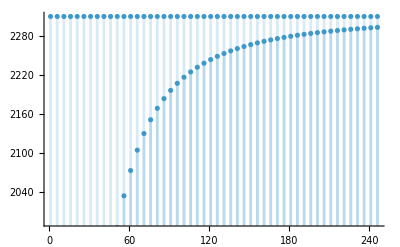

```mathematica
DiscretePlot[With[{g=4},{res,Chop@N[qresvaltrig/. {κ-> 4+k} ]}],{k,1,250,5}]
```

```mathematica
Clear[res, qres, qresval, qresvaltrig,integrableirrepsA]
```

#### Quantum dimensions (symbolic input )

Usual (classical) dimension:

```mathematica
res=DimensionIrrepLie ["A3",{a,b,c}]
```

1/12 (1+a) (1+b) (2+a+b) (1+c) (2+b+c) (3+a+b+c)

Quantum dimension:

```mathematica
qres=DimensionIrrepLie ["A3",{a,b,c},q]
```

(qnum[1+a,q] qnum[1+b,q] qnum[2+a+b,q] qnum[1+c,q] qnum[2+b+c,q] qnum[3+a+b+c,q])/(qnum[1,q]^3 qnum[2,q]^2 qnum[3,q])

Nicer output:

```mathematica
qres /. {qnum[n_,q] :> Subscript[Row[{"(",n,")"}],q]}
```

((1+a)_q (1+b)_q (2+a+b)_q (1+c)_q (2+b+c)_q (3+a+b+c)_q)/((1)_q^3 (2)_q^2 (3)_q)

Explicit result in terms of q:

```mathematica
qresval=qres/.{qnum[n_,q]:> (q^n - q^(-n))/(q-q^(-1))}
```

((-q^(-1-a)+q^(1+a)) (-q^(-1-b)+q^(1+b)) (-q^(-2-a-b)+q^(2+a+b)) (-q^(-1-c)+q^(1+c)) (-q^(-2-b-c)+q^(2+b+c)) (-q^(-3-a-b-c)+q^(3+a+b+c)))/((-1/q+q)^3 (-1/q^2+q^2)^2 (-1/q^3+q^3))

Assume that q is a complex root of unity.
The following command is slow when the input (irrep) is not numeric:

```mathematica
qresvaltrig=FullSimplify[ExpToTrig[Expand[Together[qresval]/.{q->Exp[(ⅈ π)/κ]}]],Assumptions->κ>0]//PowerExpand(* Value for q, a root of unity *)
```

(Csc[π/κ]^6 Sec[π/κ]^2 Sin[π/κ+(a π)/κ] Sin[π/κ+(b π)/κ] Sin[(2 π)/κ+((a+b) π)/κ] Sin[π/κ+(c π)/κ] Sin[(2 π)/κ+((b+c) π)/κ] Sin[(3 π)/κ+((a+b+c) π)/κ])/(4+8 Cos[(2 π)/κ])

For the following choice of a,b,c, the integer κ should be large enough (setting κ = 4 + k, the level k should be equal or larger than 8):

```mathematica
(qresvaltrig/. {a-> 3,b->4,c->1})/. κ->11
```

0

```mathematica
(qresvaltrig/. {a-> 3,b->4,c->1})/. κ->12
```

(√3 (-1+√3)^3 (1+√3)^8)/(8 (4+4 √3))

```mathematica
%//N
```

24.1244

```mathematica
Clear[res, qres, qresval, qresvaltrig]
```

#### Quantum dimensions : another example (G2)

```mathematica
qres=DimensionIrrepLie ["G2",{2,3},q]
```

(qnum[13/3,q] qnum[17/3,q] qnum[7,q] qnum[10,q])/(qnum[1/3,q] qnum[1,q] qnum[5/3,q] qnum[2,q])

A nicer output (Warning: One has to use RuleDelayed (:>) in the following input, not Rule ( ->) ):

```mathematica
qres /. {qnum[n_,q] :> Subscript[Row[{"(",n,")"}],q]}
```

((13/3)_q (17/3)_q (7)_q (10)_q)/((1/3)_q (1)_q (5/3)_q (2)_q)

The quantum dimension in terms of the formal variable q:

```mathematica
qresval=qres/.{qnum[n_,q]:> (q^n - q^(-n))/(q-q^(-1))}
```

((-1/q^(13/3)+q^(13/3)) (-1/q^(17/3)+q^(17/3)) (-1/q^7+q^7) (-1/q^10+q^10))/((-1/q^(1/3)+q^(1/3)) (-1/q+q) (-1/q^(5/3)+q^(5/3)) (-1/q^2+q^2))

```mathematica
Limit[%,q->1](* Checking the classical limit *)
```

1547

The quantum dimension when q is a root of unity:

```mathematica
qresvaltrig=FullSimplify[ExpToTrig[Expand[Together[qresval]/.{q->Exp[(ⅈ π)/κ]}]]]
```

1/((ⅇ^((ⅈ π)/κ))^(2/3))(1+2 Cos[(2 π)/κ]+2 Cos[(6 π)/κ]+2 Cos[(10 π)/κ]) (22 (ⅇ^((ⅈ π)/κ))^(1/3) Cos[π/κ]+8 Cos[π/κ]^2 Cos[(2 π)/κ]^2 (-1+2 Cos[(2 π)/κ]) (1+2 Cos[(2 π)/κ])^2+8 ⅈ Cos[π/κ]^3 (1-2 Cos[(2 π)/κ])^2 (Sin[π/κ]+Sin[(5 π)/κ])+(ⅇ^((ⅈ π)/κ))^(1/3) (11 (ⅇ^((ⅈ π)/κ))^(1/3)+19 Cos[(3 π)/κ]+15 Cos[(5 π)/κ]+9 Cos[(7 π)/κ]+5 Cos[(9 π)/κ]+2 Cos[(11 π)/κ]+2 (ⅇ^((ⅈ π)/κ))^(1/3) (11 Cos[(2 π)/κ]+9 Cos[(4 π)/κ]+6 Cos[(6 π)/κ]+4 Cos[(8 π)/κ]+2 Cos[(10 π)/κ]+Cos[(12 π)/κ])+ⅈ (Sin[(3 π)/κ]+Sin[(5 π)/κ]+Sin[(7 π)/κ]+Sin[(9 π)/κ])))

```mathematica
%/. κ -> 12  (* a particular choice for κ. Warning: κ should be large enough for this irrep to exist *)
```

1/((ⅇ^((ⅈ π)/12))^(2/3))(3/4 (-1+√3) (1+√3)^4+(ⅈ (1-√3)^2 (1+√3)^3 ((-1+√3)/(2 √2)+(1+√3)/(2 √2)))/(2 √2)+(11 (1+√3) (ⅇ^((ⅈ π)/12))^(1/3))/(√2)+(ⅇ^((ⅈ π)/12))^(1/3) (7 √2+(3 (-1+√3))/(√2)-(1+√3)/(√2)+ⅈ (√2+(1+√3)/(√2))+11 (ⅇ^((ⅈ π)/12))^(1/3)+2 (3/2+(9 √3)/2) (ⅇ^((ⅈ π)/12))^(1/3)))

```mathematica
Chop[N[ %]]
```

91.4794

The quantum dimension in terms of QPochhammer symbol:

```mathematica
qres/. {qnum[n_,q]->-(q^(1-n) QPochhammer[q^2,q^2,n])/((-1+q^2) QPochhammer[q^2,q^2,-1+n])}//Simplify
```

(QPochhammer[q^2,q^2,-2/3] QPochhammer[q^2,q^2,2/3] QPochhammer[q^2,q^2,13/3] QPochhammer[q^2,q^2,17/3] QPochhammer[q^2,q^2,7] QPochhammer[q^2,q^2,10])/(q^22 QPochhammer[q^2,q^2,1/3] QPochhammer[q^2,q^2,5/3] QPochhammer[q^2,q^2,2] QPochhammer[q^2,q^2,10/3] QPochhammer[q^2,q^2,14/3] QPochhammer[q^2,q^2,6] QPochhammer[q^2,q^2,9])

```mathematica
%//FunctionExpand
```

((1-q^14) (1-q^20) (1-(q^2)^(13/3)) (1-(q^2)^(17/3)))/(q^22 (1-q^2) (1-q^4) (1-(q^2)^(1/3)) (1-(q^2)^(5/3)))

```mathematica
Chop[N[ %/.{q->Exp[(ⅈ π)/12]}],10^-8]
```

91.4794

```mathematica
Clear[res,qres, qresval, qresvaltrig]
```

### Possible Issues

Study of quantum dimensions: DimensionIrrepLie["G",ruplet,q] treats the third argument as the literal symbol q.
If your session already defines a value for q (e.g. q = 5), that value will propagate into the output (you'll see qnum[⋯, 5]).
To avoid unintended substitutions, ensure that q is unassigned before calling the function (Clear[q];); alternatively, call the function in a localized environment (Block[{q}, DimensionIrrepLie["G",ruplet,q]]).

In the case of quantum dimensions at roots of unity, the value of kappa in q = Exp(I Pi / kappa) should be large enough for the chosen representation to exist (integrability condition).

In the case of quantum dimensions at roots of unity, the simplification of the generated trigonometric expressions can be slow.